# Dirac Potential and EDAD2 parameters set

```mathematica
mp = 938.2723;
amu=931.502;
m23F=21423.077578;
m25F =23294.116;
ℏ=197.3269788; (* MeV fm /c^2*)
EDAD2Par={
(*1*){24.19272,-134.7303,256.5835,-213.0657,66.40990,13.70940,-20.41843,7.075551},
(*2*){-7.996201,44.47337,-82.09251,65.81308,-19.58522,0.4233910,-.4699721,0.4984338},
(*3*){11.75859,-57.09638,101.8926,-80.29220,23.48163,2.467907,-4.579546,2.374239},
(*4*){2.983074  100,-1.504920  1000,2.599143  1000,-1.941105  1000,5.424824  100,8.374511  10,-9.919251  10,1.445072  10},(*5*){6.406925 ,-3.597956  10,6.812012  10,-5.464849  10,1.708801  10,4.927107 ,-6.184351 ,1.744822 },
(*6*){-1.390377  10,6.935514  10,-1.199980  100,9.329035  10,-2.795019  10,5.004301 ,-1.251040 ,1.823093 },
(*7*){2.049078  10,-1.113498  100,2.078705  100,-1.672745  100,4.995035  10,8.214217 ,-1.343718  10,5.939270 },
(*8*){-7.614336 ,4.246558  10,-7.769977  10,6.164974  10,-1.820658  10,1.267682  0.1,3.590679  0.01,3.889028  0.1},
(*9*){1.594873  10,-7.751876  10,1.397383  100,-1.114398  100,3.316194  10,2.398806 ,-4.620640 ,2.264939 },
(*10*){-6.784464  10,4.019749  100,-7.220732  100,5.760043  100,-1.782302  100,-5.040930  10,7.959955  10,-2.771373  10},(*11*){-4.752988 ,8.257322 ,-4.803583 ,-6.860379  0.1,2.084371 ,1.283227  10,-1.491639  10,4.350842 },
(*12*){-1.485421  10,8.094352  10,-1.543248  100,1.272100  100,-3.885699  10,7.132415 ,-1.182152  10,6.334432 },
(*13*){2.144962  10,-1.353171  100,2.755466  100,-2.605909  100,9.401126  10,1.111419  10,-3.690369  10,1.774420  10},
(*14*){-2.062301  0.01,9.013484  0.1,-7.911715  0.1,3.133864 ,-1.699538 ,-4.994396  0.1,0.000000 ,0.000000 },
(*15*){1.658819 ,-4.383188 ,2.324352 ,-1.355365  10,9.547320 ,-1.238569 ,0.000000 ,0.000000 },
(*16*){4.877378  10,-2.516897  100,4.693758  100,-3.746622  100,1.099748  100,-7.058762  0.1,1.635300  10,-1.092225  10},
(*17*){-8.331280  0.01,1.215059 ,-1.131819 ,3.421545 ,-2.214773 ,-1.626730  0.1,0.000000 ,0.000000 },
(*18*){-3.889444 ,-3.422776 ,6.241782 ,-4.801031 ,2.252025 ,1.982958 ,0.000000 ,0.000000 },
(*19*){1.221290 ,-7.093230 ,7.266262 ,-2.368339 ,-5.509552  10,6.461826  10,0.000000 ,0.000000 },
(*20*){2.000496 ,-3.189503 ,2.003387 ,-2.493790  10,3.281269  10,-1.877461  10,0.000000 ,0.000000 },
(*21*){3.119507  10,-1.996679  10,2.433381 ,-1.527184  10,5.443329 ,2.462658 ,0.000000 ,0.000000 },
(*22*){0.000000 ,0.000000 ,0.000000 ,0.000000 ,0.000000 ,0.000000 ,0.000000 ,0.000000 }
};
EcmP[A_,T_]:=Module[{Pproton, β,γ },
Pproton={mp+T, √(2mp T+T^2)};
β=Pproton[[2]]/(Pproton[[1]]+A*amu);
γ=1/(√(1-β^2));
{γ,- γ β}.Pproton
]
EcmA[A_,T_]:=Module[{Pproton, Ptarget, β,γ },
Ptarget={A*amu, 0};
Pproton={mp+T, √(2mp T+T^2)};
β=Pproton[[2]]/(Pproton[[1]]+A*amu);
γ=1/(√(1-β^2));
{γ,- γ β}.Ptarget
]
prePotential[A_,T_]:=Module[{x,y,J1,J2, fact},
x=1000/EcmP[A,T];
y = A/(A+20);
J1={1, x, x^2, x^3, x^4, y , y^2, y^3};
J2={x y, x^2 y, x y^2};
fact=1.00;
{
(*Real Vector vol + scalar, Real Vector vol, Real Vector vol*) {-100(EDAD2Par[[1]].J1+EDAD2Par[[19,1;;3]].J2),(EDAD2Par[[2]].J1+EDAD2Par[[14,1;;3]].J2)A^(1/3)fact,(EDAD2Par[[3]].J1+EDAD2Par[[14,4;;6]].J2)0.7},
(*Img Vector vol + scalar, Img Vector vol, Img Vector vol*) {-15(EDAD2Par[[4]].J1+EDAD2Par[[19,4;;6]].J2),(EDAD2Par[[5]].J1+EDAD2Par[[15,1;;3]].J2)A^(1/3)fact,(EDAD2Par[[6]].J1+EDAD2Par[[15,4;;6]].J2)0.7},
(*Real Scalar vol - scalar, Real Scalar vol, Real Scalar vol*) {700(EDAD2Par[[7]].J1+EDAD2Par[[20,1;;3]].J2),(EDAD2Par[[8]].J1+EDAD2Par[[17,1;;3]].J2)A^(1/3)fact,(EDAD2Par[[9]].J1+EDAD2Par[[17,4;;6]].J2)0.7},
(*Img Scalar vol - scalar, Img Scalar vol, Img Scalar vol*) {-150(EDAD2Par[[10]].J1+EDAD2Par[[20,4;;6]].J2),(EDAD2Par[[11]].J1+EDAD2Par[[18,1;;3]].J2)A^(1/3)fact,(EDAD2Par[[12]].J1+EDAD2Par[[18,4;;6]].J2)0.7},
(*Img vector surf, Img scalar surf, Real vector surf, Real scalar surf*) {-100(EDAD2Par[[13]].J1+EDAD2Par[[21,1;;3]].J2),100(EDAD2Par[[16]].J1+EDAD2Par[[21,4;;6]].J2),0,0}
}
]
Potential[A_,T_]:=Module[{preP},
preP=prePotential[A,T];
{
(*Real Vector vol, Real Vector vol/surf, Real Vector vol/surf*){(preP[[1,1]]+preP[[3,1]])/2,preP[[1,2]],preP[[1,3]]},
(*Real Scalar vol, Real Scalar vol/surf, Real Scalar vol/surf*){(preP[[1,1]]-preP[[3,1]])/2,preP[[3,2]],preP[[3,3]]},
(*Img Vector vol, Img Vector vol/surf, Img Vector vol/surf*){(preP[[2,1]]+preP[[4,1]])/2,preP[[2,2]],preP[[2,3]]},
(*Img Scalar vol, Img Scalar vol/surf, Img Scalar vol/surf*){(preP[[2,1]]-preP[[4,1]])/2,preP[[4,2]],preP[[4,3]]},
(*Real Vector surf*){preP[[5,3]],preP[[1,2]],preP[[1,3]]},
(*Real Scalar surf*){preP[[5,4]],preP[[3,2]],preP[[3,3]]},
(*Img Vector surf*){preP[[5,1]],preP[[2,2]],preP[[2,3]]},
(*Img Scalar surf*){preP[[5,2]],preP[[4,2]],preP[[4,3]]}
}
]
PrintPotential[A_,T_]:=Module[{p,pp},
p=Potential[A,T];
pp=Transpose[Join[{{Style["A="<>ToString[A]<>", T="<>ToString[T]<>"A MeV",Red],"Real Vec vol","Real Scal vol","Img Vec vol", "Img Scal vol", "Real Vec surf","Real Scal surf","Img Vec surf","Img Scal surf"}},Transpose[Join[{{"V/W","R","A"}},p]]]];
pp[[6,3]]=pp[[6,3]]/A^(1/3);pp[[6,4]]="Recoil Vect";
pp[[7,3]]=pp[[7,3]]/A^(1/3);pp[[7,4]]=EcmA[A,T]/(EcmA[A,T]+EcmP[A,T]);
pp[[8,3]]=pp[[8,3]]/A^(1/3);pp[[8,4]]="Recoil Scal";
pp[[9,3]]=pp[[9,3]]/A^(1/3);pp[[9,4]]=A*amu/(EcmA[A,T]+EcmP[A,T]);
TableForm[pp]
]
fV[r_,R_,a_]:=(Cosh[R/a]-1)/(Cosh[R/a]+Cosh[r/a]-2)
fS[r_,R_,a_]:=((Cosh[R/a]-1)(Cosh[r/a]-1))/(Cosh[R/a]+Cosh[r/a]-2)^2
PotentialFunc[A_,T_,r_]:=Module[{p,RecoilScal,RecoilVect},
p=Potential[A,T];
RecoilVect=EcmA[A,T]/(EcmA[A,T]+EcmP[A,T]);
RecoilScal=A*amu/(EcmA[A,T]+EcmP[A,T]);
{
(* Real Vect *) RecoilVect(p[[1,1]]fV[r,p[[1,2]],p[[1,3]]]+p[[5,1]]fS[r,p[[5,2]],p[[5,3]]]),
(* Real Scal *) RecoilScal(p[[2,1]]fV[r,p[[2,2]],p[[2,3]]]+p[[6,1]]fS[r,p[[6,2]],p[[6,3]]]),
(* img Vect *) RecoilVect(p[[3,1]]fV[r,p[[3,2]],p[[3,3]]]+p[[7,1]]fS[r,p[[7,2]],p[[7,3]]]),
(* Img Scal *) RecoilScal(p[[4,1]]fV[r,p[[4,2]],p[[4,3]]]+p[[8,1]]fS[r,p[[8,2]],p[[8,3]]])
}
]
DisplayPotential[A_,Z_,T_,rc_,n_,h_,mode_]:=Module[
{dr,k},
dr=If[mode==1,h (A-1)/A,h];
Print[PrintPotential[A,T]];
k=PotentialFunc[A,T,0];
Plot[Evaluate[PotentialFunc[A,T,r]],{r,0,10},
PlotLabel->Style["A="<>ToString[A]<>", Z="<>ToString[Z]<>", T="<>ToString[T]<>" MeV/nucleon\n #Step="<>ToString[n]<>", dr="<>ToString[dr]<>" fm, R_c="<>ToString[rc]<>" fm",20],
Epilog->{
Text[Style["Real Vector",Red,20],{8,k[[1]]0.5}],
Text[Style["Real Scalar",Orange,20],{8,k[[2]]0.5}],
Text[Style["Img Victor",Blue,20],{8,k[[3]]0.5}],
Text[Style["Img Scalar",Purple,20],{8,k[[4]]0.5}]},
PlotRange->All,PlotStyle->{Red(*RV*),Orange(*RS*),Blue(*IV*),Purple(*IS*)},
GridLines->Automatic,Axes->False,GridLinesStyle->Directive[Gray,Dashed],
Frame->True,FrameLabel->{Style["r [fm]",20],Style["Potential [MeV]",20]},
ImageSize->600]
(* Scale Potential *)
(*Table[PotentialFunc[A,T,r][[{2,3}]],{r,0,n dr,dr}]*)
(* Vector Potential *)
(*Table[PotentialFunc[A,T,r][[{1,3}]],{r,0,n dr,dr}]*)
]
```

A=23, T=289A MeV | V/W | R | A
Real Vec vol | 291.86 | 2.85171 | 0.570809
Real Scal vol | -395.974 | 2.82731 | 0.60445
Img Vec vol | -93.1236 | 3.25155 | 0.613283
Img Scal vol | 93.6212 | 3.25763 | 0.61498
Real Vec surf | 0 | 1.00276 | Recoil Vect
Real Scal surf | 0 | 0.994177 | 0.946975
Img Vec surf | 25.9691 | 1.14336 | Recoil Scal
Img Scal surf | -36.4026 | 1.14549 | 0.946397

A=25, T=277A MeV | V/W | R | A
Real Vec vol | 294.783 | 2.94714 | 0.578211
Real Scal vol | -399.262 | 2.92252 | 0.611331
Img Vec vol | -87.6881 | 3.36996 | 0.605496
Img Scal vol | 85.4481 | 3.38421 | 0.59926
Real Vec surf | 0 | 1.00791 | Recoil Vect
Real Scal surf | 0 | 0.999487 | 0.951348
Img Vec surf | 24.8899 | 1.15251 | Recoil Scal
Img Scal surf | -33.8209 | 1.15739 | 0.950875

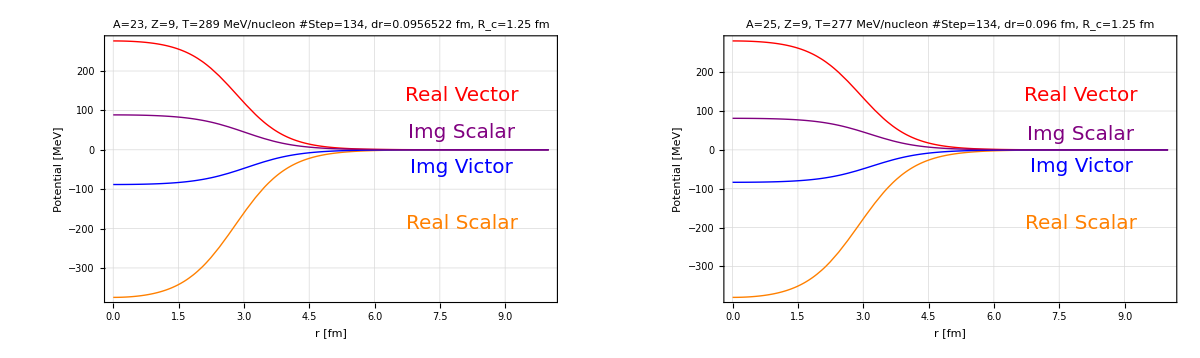

```mathematica
k1=DisplayPotential[23,9,289,1.25,134,0.1,1];
k2=DisplayPotential[25,9,277,1.25,134,0.1,1];
GraphicsGrid[{{k1,k2}},ImageSize->1200]
```

```mathematica
PotentialFunc[25,277,0]
```

{280.442,-379.648,-83.4219,81.2505}

## Convert UV and US to SE potential Numerically

```mathematica
CoulPot[A_,Z_,rc_,r_]:=Module[{Coul,R},
R=rc A^(1/3);
Coul=1.44 Z ;
Piecewise[{{(1.5/R-0.5/R^3 r^2)Coul,r<R},{Coul/r,r≥ R}}]
]
DeriV[listV_,dr_]:=Join[
{{listV[[1,1]],1/(12 dr)(-25 listV[[1,2]]+48 listV[[2,2]]-36 listV[[3,2]]+16 listV[[4,2]]-3listV[[5,2]])},
{listV[[2,1]],1/(12 dr)(-3 listV[[1,2]]-10 listV[[2,2]]+18 listV[[3,2]]-6 listV[[4,2]]+listV[[5,2]])}},
Table[{listV[[i,1]],1/(12 dr)(listV[[i-2,2]]-8listV[[i-1,2]]+8listV[[i+1,2]]-listV[[i+2,2]])},{i,3,Length[listV]-2}],
{{listV[[-2,1]],1/(12 dr)(- listV[[-5,2]]+6 listV[[-4,2]]-18 listV[[-3,2]]+10 listV[[-2,2]]+3listV[[-1,2]])},
{listV[[-1,1]],1/(12 dr)(3 listV[[-5,2]]-16listV[[-4,2]]+36 listV[[-3,2]]-48 listV[[-2,2]]+25listV[[-1,2]])}}
]
RePot[potlist_]:=Table[{potlist[[i,1]],Re[potlist[[i,2]]]},{i,1,Length[potlist]}]
ImPot[potlist_]:=Table[{potlist[[i,1]],Im[potlist[[i,2]]]},{i,1,Length[potlist]}]
```

```mathematica
EDAD2[A_,Z_,T_,rc_,n_,h_,mode_]:=Module[
{dr,Ep,EA,RED,DR,DUV,DUS,DCoulPot,DVZ,DB,DB2,DPerey,DBDr,DpreDarwin,DpreDarwin2,DDarwin,DUcent,DULS,},
dr=If[mode==1,h(A-1)/A,h];
Ep=EcmP[A,T];
EA=EcmA[A,T];
RED=EA Ep/(Ep+EA);
DR=Table[r,{r,0,n dr,dr}];
DUV=Table[{r,PotentialFunc[A,T,r][[1]]+ⅈ PotentialFunc[A,T,r][[3]]},{r,0,n dr,dr}];
DUS=Table[{r,PotentialFunc[A,T,r][[2]]+ⅈ PotentialFunc[A,T,r][[4]]},{r,0,n dr,dr}];
DCoulPot=Table[{r,CoulPot[A,Z,rc,r-0.1]},{r,0,n dr,dr}];
DVZ=Table[{DR[[i]],DCoulPot[[i,2]] RED/Ep},{i,1,n}];
DB=Table[{DR[[i]],(DUS[[i,2]]-DUV[[i,2]]-DVZ[[i,2]])/(Ep+mp)},{i,1,n}];
DB2=Table[{DR[[i]],DB[[i,2]]+1},{i,1,n}];
DPerey=Table[{DR[[i]],Sqrt[DB2[[i,2]]]},{i,1,n}];
DBDr=DeriV[DB,dr];
DpreDarwin=DeriV[Table[{DR[[i]],DR[[i]]^2 DBDr[[i,2]]},{i,1,n}],dr];
DpreDarwin2=
Join[{{DR[[1]],2((-DpreDarwin[[2,2]])/(2 (n dr)^2 Abs[DB2[[2,2]]])+0.75 (DBDr[[2,2]]/Abs[DB2[[2,2]]])^2)-(-DpreDarwin[[3,2]])/(2 (n dr)^2 Abs[DB2[[3,2]]])+0.75 (DBDr[[3,2]]/Abs[DB2[[3,2]]])^2}},
Table[{DR[[i]],(-DpreDarwin[[i,2]])/(2 (n dr)^2 Abs[DB2[[i,2]]])+0.75 (DBDr[[i,2]]/Abs[DB2[[i,2]]])^2},{i,2,n}]];
DDarwin=Table[{DR[[i]],DpreDarwin2[[i,2]] 197.3286^2/RED},{i,1,n}];
DUcent=Table[{DR[[i]],DUV[[i,2]] Ep/RED+DUS[[i,2]] mp/RED+(DUS[[i,2]]^2-DUV[[i,2]]^2)/(2 RED)- (DVZ[[i,2]]^2+2 DUV[[i,2]] DVZ[[i,2]])/(2 RED)+DDarwin[[i,2]]},{i,1,n}];
DULS=Join[{{DR[[1]],2((- DBDr[[2,2]])/(2 RED DR[[2]] DB2[[2,2]])197.3286^2)-((- DBDr[[3,2]])/(2 RED DR[[3]] DB2[[3,2]])197.3286^2)}},Table[{DR[[i]],(- DBDr[[i,2]])/(2 RED DR[[i]] DB2[[i,2]])197.3286^2},{i,2,n}]];
{DUcent,DULS,DDarwin,DCoulPot,DPerey,{A,Z,T,rc,n,dr}}
]
```

## SandBox

```mathematica
n=178;
F23Dirac=EDAD2[23,9,289,1.25,n,0.1,1];
F25Dirac=EDAD2[25,8,277,1.25,n,0.1,1];
```

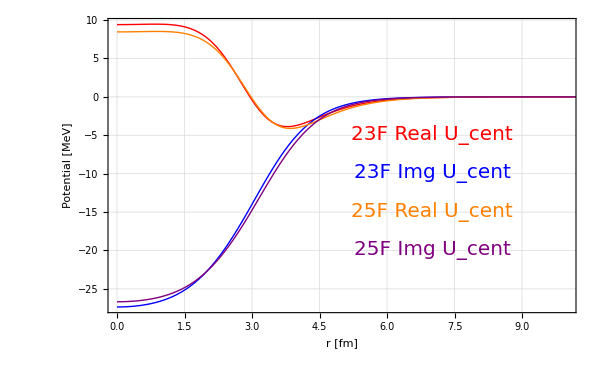

```mathematica
ListPlot[{
RePot[F23Dirac[[1]]],
ImPot[F23Dirac[[1]]],
RePot[F25Dirac[[1]]],
ImPot[F25Dirac[[1]]]
},
Epilog->{
Text[Style["23F Real U_cent",Red,20],{7,-5}],
Text[Style["23F Img U_cent",Blue,20],{7,-10}],
Text[Style["25F Real U_cent",Orange,20],{7,-15}],
Text[Style["25F Img U_cent",Purple,20],{7,-20}]
},
GridLines->Automatic,ImageSize->600,GridLinesStyle->Directive[Gray, Dashed],
Axes->False,Frame->True,FrameLabel->{Style["r [fm]",20],Style["Potential [MeV]",20]},
Joined->True,PlotRange->{{0,10},All},PlotStyle->{Red,Blue,Orange,Purple}]
```

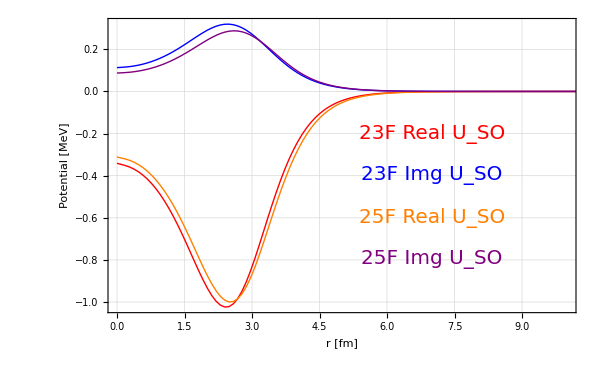

```mathematica
ListPlot[{
RePot[F23Dirac[[2]]],
ImPot[F23Dirac[[2]]],
RePot[F25Dirac[[2]]],
ImPot[F25Dirac[[2]]]
},
Epilog->{
Text[Style["23F Real U_SO",Red,20],{7,-0.2}],
Text[Style["23F Img U_SO",Blue,20],{7,-0.4}],
Text[Style["25F Real U_SO",Orange,20],{7,-0.6}],
Text[Style["25F Img U_SO",Purple,20],{7,-0.8}]
},
GridLines->Automatic,ImageSize->600,GridLinesStyle->Directive[Gray, Dashed],
Axes->False,Frame->True,FrameLabel->{Style["r [fm]",20],Style["Potential [MeV]",20]},
Joined->True,PlotRange->{{0,10},All},PlotStyle->{Red,Blue,Orange,Purple}]
```

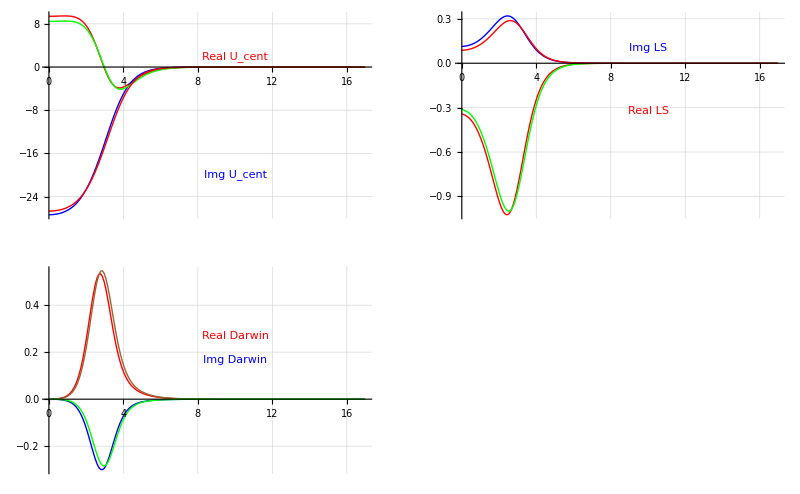

```mathematica
g1=ListPlot[{
RePot[F23Dirac[[3]]],
ImPot[F23Dirac[[3]]],
RePot[F25Dirac[[3]]],
ImPot[F25Dirac[[3]]]
},
Epilog->{Text[Style["Real Darwin",Red],{10,MaxDDarwin=Max[Table[Re[F23Dirac[[3,i,2]]],{i,1,n}]]0.5}],Text[Style["Img Darwin",Blue],{10,MaxDDarwin -0.1}]},
GridLines->Automatic,
Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Brown,Green} ];

g2=ListPlot[{
RePot[F23Dirac[[1]]],
ImPot[F23Dirac[[1]]],
RePot[F25Dirac[[1]]],
ImPot[F25Dirac[[1]]]
},
Epilog->{Text[Style["Real U_cent",Red],{10,Mean[Table[Re[F23Dirac[[1,i,2]]],{i,1,IntegerPart[n/2]}]]}],
Text[Style["Img U_cent",Blue],{10,Mean[Table[Im[F23Dirac[[1,i,2]]],{i,1,IntegerPart[n/2]}]]-10}]},
GridLines->Automatic,
Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Green} ];
g3=ListPlot[{
RePot[F23Dirac[[2]]],
ImPot[F23Dirac[[2]]],
RePot[F25Dirac[[2]]],
ImPot[F25Dirac[[2]]]
},
Epilog->{Text[Style["Real LS",Red],{10,Mean[Table[Re[F23Dirac[[2,i,2]]],{i,1,IntegerPart[n/2]}]]}],
Text[Style["Img LS",Blue],{10,Mean[Table[Im[F23Dirac[[2,i,2]]],{i,1,IntegerPart[n/2]}]]}]},
GridLines->Automatic,
Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Green} ];
GraphicsGrid[{
{g2,g3},{g1}
},ImageSize->800,PlotLabel->"A="<>ToString[A]<>", Z="<>ToString[Z]<>", T="<>ToString[T]<>" MeV/nucleon, #Step="<>ToString[n]<>", dr="<>ToString[dr]<>" fm, R_c="<>ToString[rc]<>" fm"]
```

```mathematica
exportCent[[2]]
```

{0.096,8.31815-26.6306 ⅈ}

```mathematica
(* export LS and Coul *)
n=178;
exportDirac=EDAD2[25,9,277,1.25,n,0.1,1];
exportCent=exportDirac[[1]];
exportLS=exportDirac[[2]];
exportCoul=exportDirac[[4]];
Export["DUcent.dat",
Table[{exportCent[[i,1]],Re[exportCent[[i,2]]],Im[exportCent[[i,2]]]},{i,1,n}]//TableForm
,"CSV"]
(*Export["DULS.dat",
Table[{exportLS[[i,1]],Re[exportLS[[i,2]]],Im[exportLS[[i,2]]], exportCoul[[i,2]]},{i,1,n}]//TableForm
,"CSV"]*)
```

DUcent.dat

```mathematica
WS[r_,V_,R_,a_]:=-V/(1+Exp[(r-R)/a])
WSD[r_,V_,R_,a_]:=(V Exp[(r-R)/a])/(1+Exp[(r-R)/a])^2
RMS[listP_]:=Module[{dr},
dr=listP[[2,1]]-listP[[1,1]];
√(Sum[listP[[i,2]] listP[[i,1]]^4 dr,{i,1,Length[listP]}]/Sum[listP[[i,2]] listP[[i,1]]^2 dr,{i,1,Length[listP]}])
]
```

{V→26.9594,R→3.11993,a→0.664702}

{Reduced χ^2,0.00160523}

{R0,1.067}

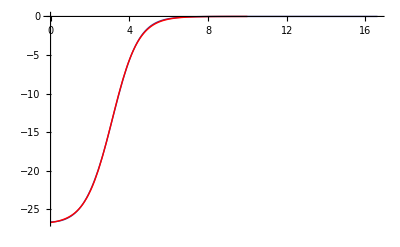

```mathematica
fit=FindFit[DUcentI,-V/(1+Exp[(r-R)/a]),{V,R,a},r]
{"Reduced χ^2",Sum[(DUcentI[[i,2]]-Evaluate[WS[DR[[i]],V,R,a]/.fit])^2/n,{i,1,n}]}
{"R0",Evaluate[R/.fit]/A^(1/3)}
Show[
ListPlot[DUcentI,Joined->True],
Plot[Evaluate[WS[r,V,R,a]/.fit],{r,0,10},PlotStyle->Red]
]
```

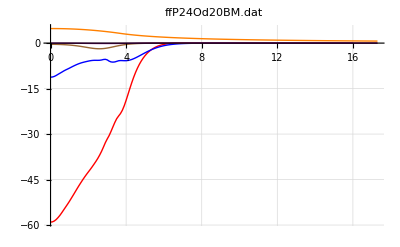

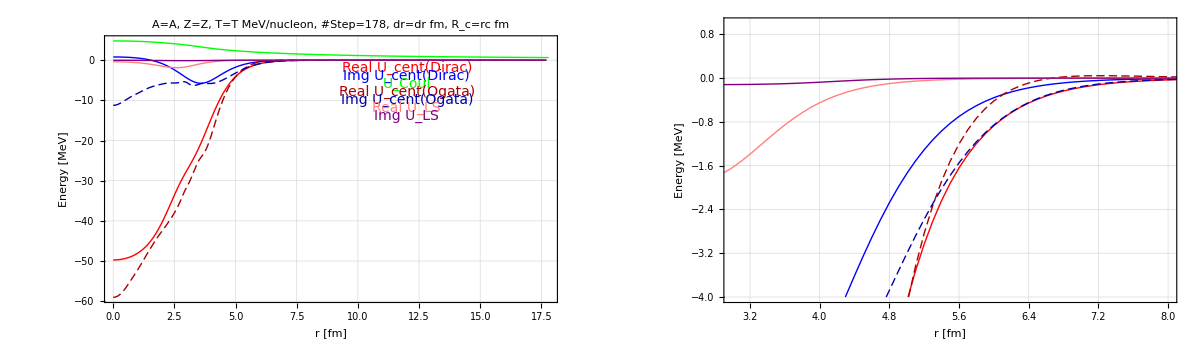

```mathematica
O24Dirac20=EDAD2[24,8,20,1.25,n,0.1,0];
O24Ogata20=GetOgata["ffP24Od20BM.dat","DULS_24O020.dat",10,1];
CompareDiracOgata[O24Dirac20,O24Ogata20]
```

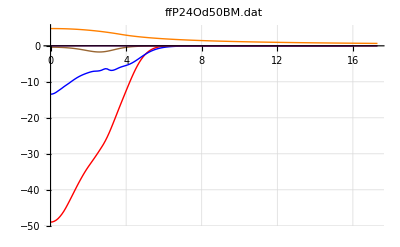

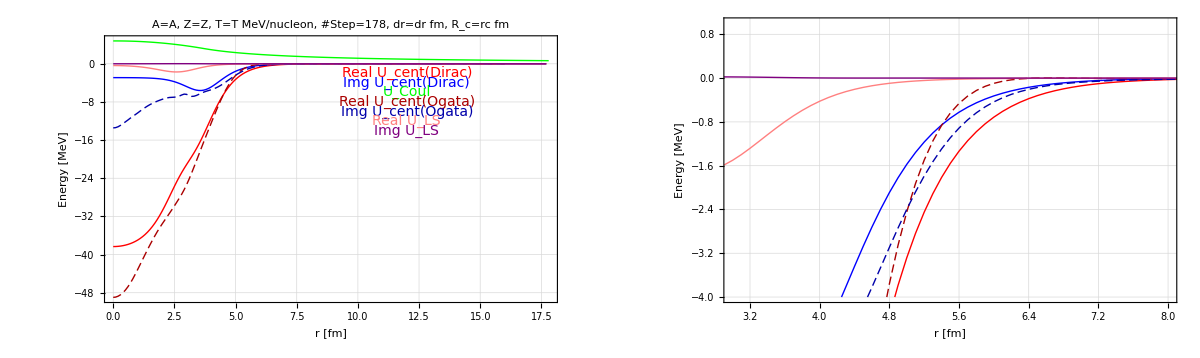

```mathematica
O24Dirac50=EDAD2[24,8,50,1.25,n,0.1,0];
O24Ogata50=GetOgata["ffP24Od50BM.dat","DULS_24O050.dat",10,1];
CompareDiracOgata[O24Dirac50,O24Ogata50]
```

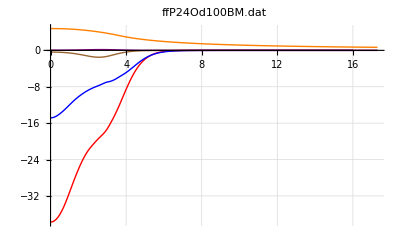

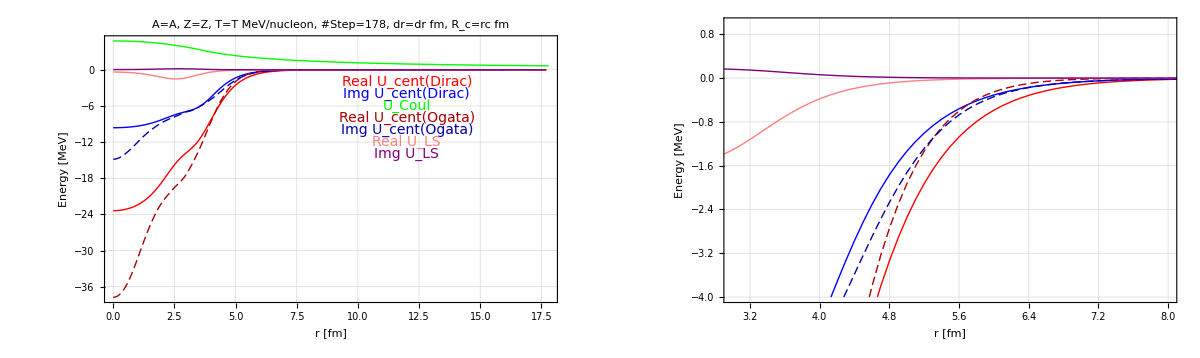

```mathematica
O24Dirac100=EDAD2[24,8,100,1.25,n,0.1,0];
O24Ogata100=GetOgata["ffP24Od100BM.dat","DULS_24O100.dat",10,1];
CompareDiracOgata[O24Dirac100,O24Ogata100]
```

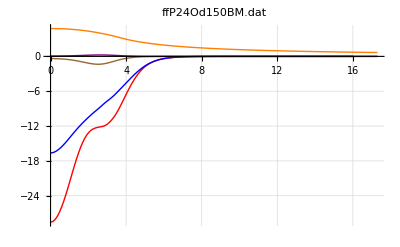

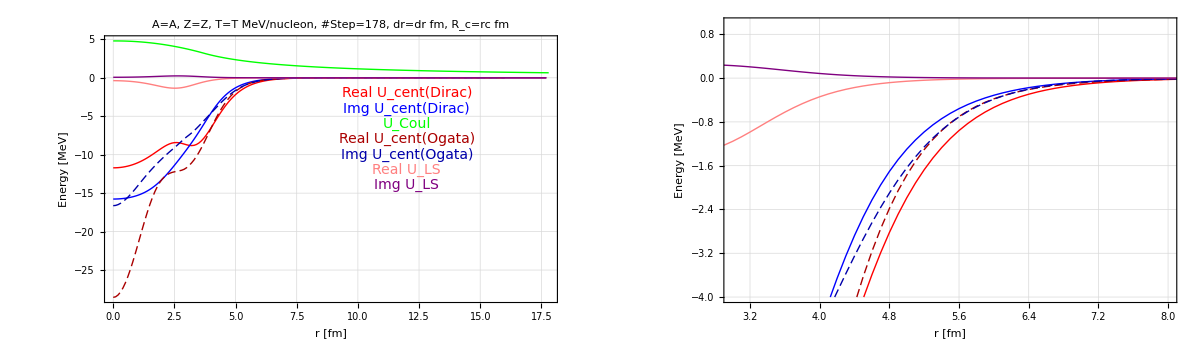

```mathematica
O24Dirac150=EDAD2[24,8,150,1.25,n,0.1,0];
O24Ogata150=GetOgata["ffP24Od150BM.dat","DULS_24O150.dat",10,1];
CompareDiracOgata[O24Dirac150,O24Ogata150]
```

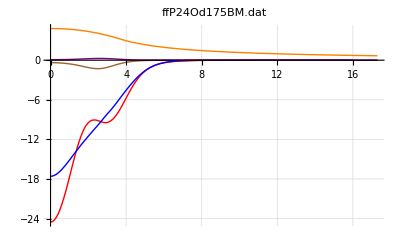

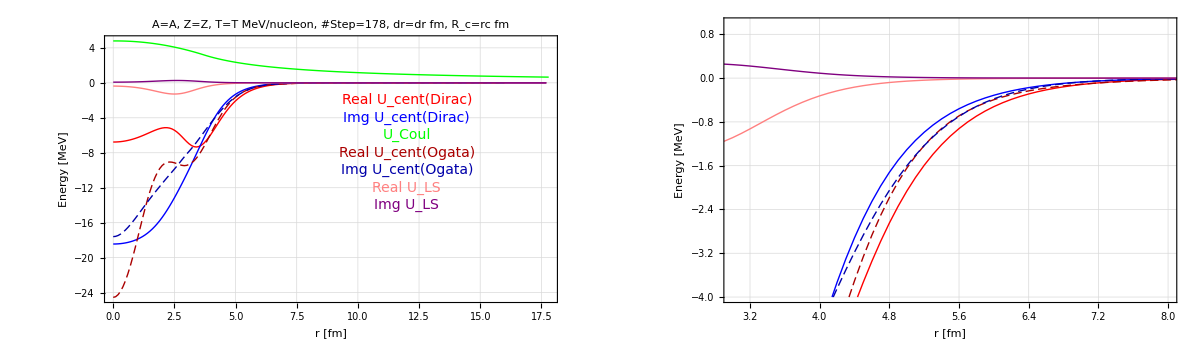

```mathematica
O24Dirac175=EDAD2[24,8,175,1.25,n,0.1,0];
O24Ogata175=GetOgata["ffP24Od175BM.dat","DULS_24O175.dat",10,1];
CompareDiracOgata[O24Dirac175,O24Ogata175]
```

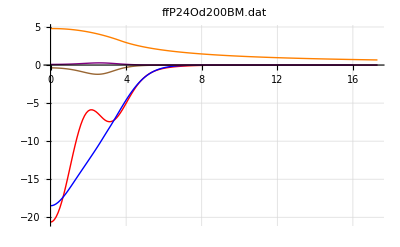

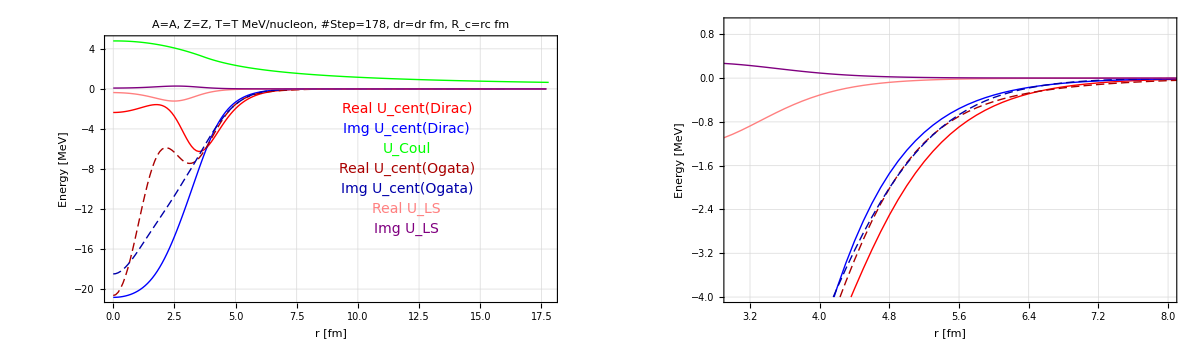

```mathematica
O24Dirac200=EDAD2[24,8,200,1.25,n,0.1,0];
O24Ogata200=GetOgata["ffP24Od200BM.dat","DULS_24O200.dat",10,1];
CompareDiracOgata[O24Dirac200,O24Ogata200]
```

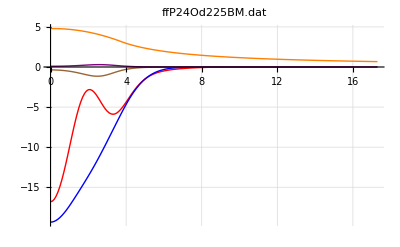

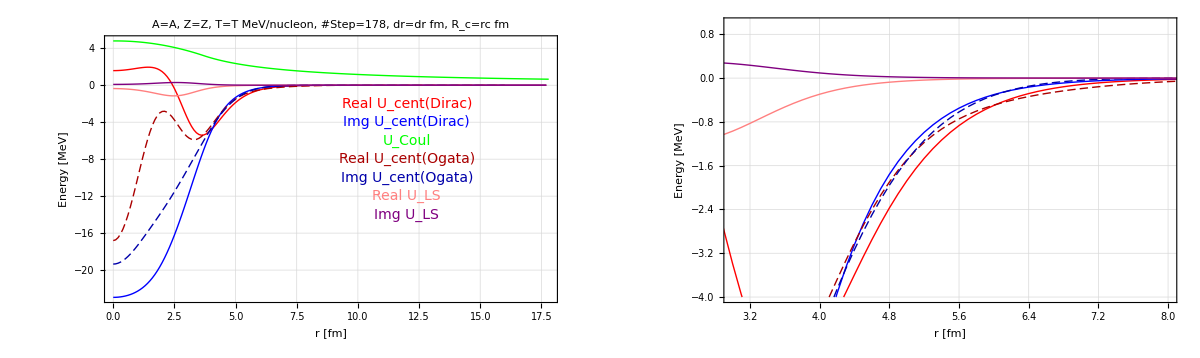

```mathematica
O24Dirac225=EDAD2[24,8,225,1.25,n,0.1,0];
O24Ogata225=GetOgata["ffP24Od225BM.dat","DULS_24O225.dat",10,1];
CompareDiracOgata[O24Dirac225,O24Ogata225]
```

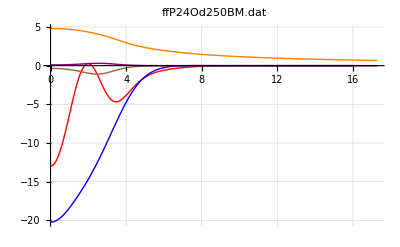

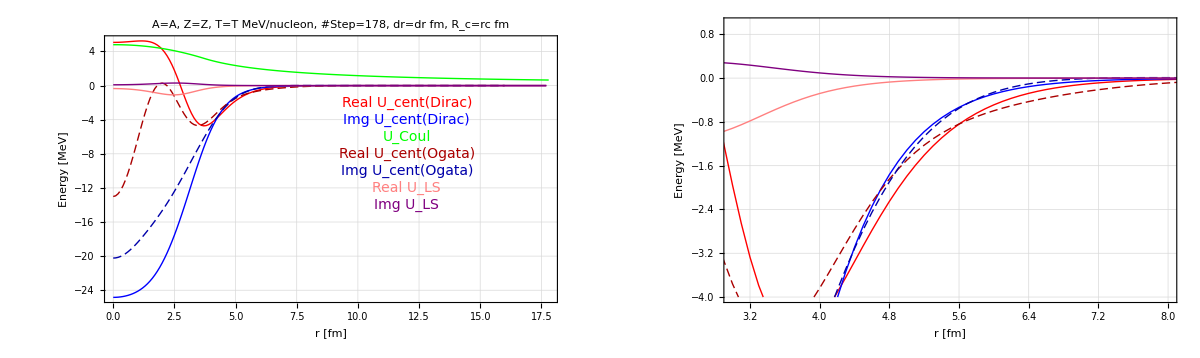

```mathematica
O24Dirac250=EDAD2[24,8,250,1.25,n,0.1,0];
O24Ogata250=GetOgata["ffP24Od250BM.dat","DULS_24O250.dat",10,1];
CompareDiracOgata[O24Dirac250,O24Ogata250]
```

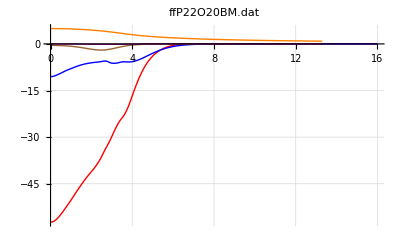

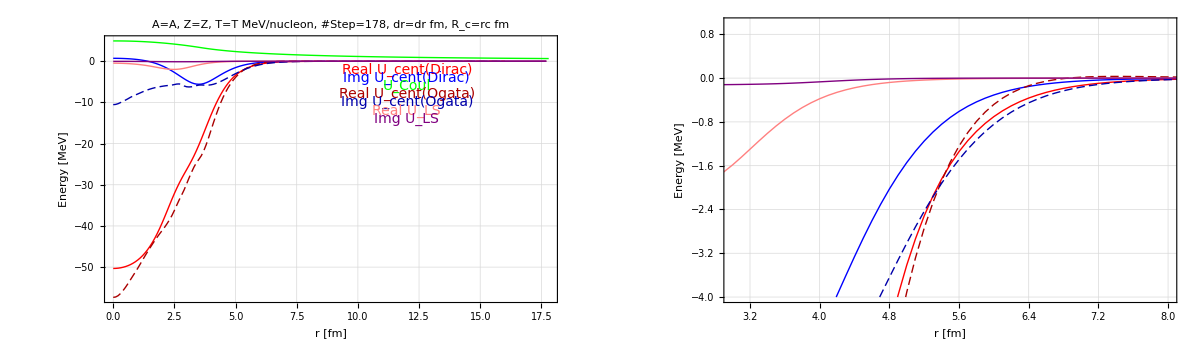

```mathematica
O22Dirac20=EDAD2[22,8,20,1.25,n,0.1,0];
O22Ogata20=GetOgata["ffP22O20BM.dat","DULS_22O020.dat",10,1];
CompareDiracOgata[O22Dirac20,O22Ogata20]
```

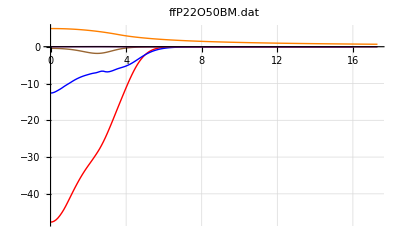

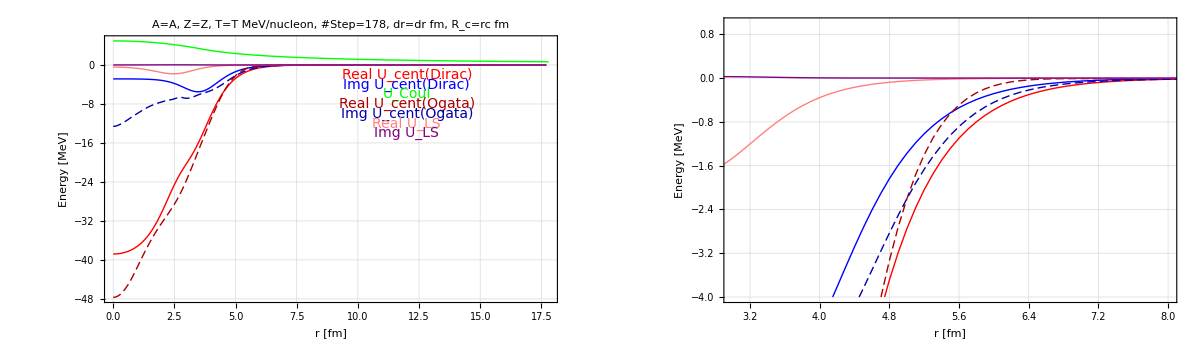

```mathematica
O22Dirac50=EDAD2[22,8,50,1.25,n,0.1,0];
O22Ogata50=GetOgata["ffP22O50BM.dat","DULS_22O050.dat",10,1];
CompareDiracOgata[O22Dirac50,O22Ogata50]
```

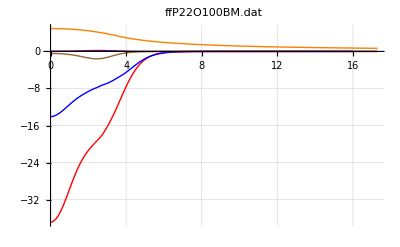

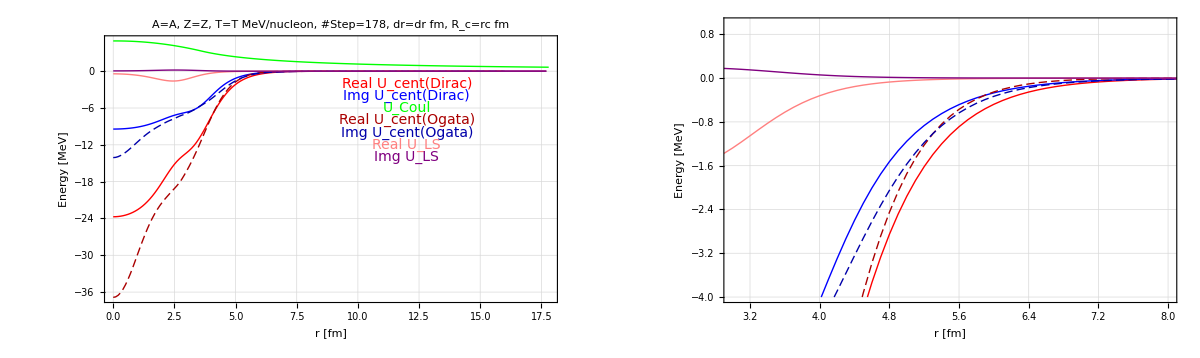

```mathematica
O22Dirac100=EDAD2[22,8,100,1.25,n,0.1,0];
O22Ogata100=GetOgata["ffP22O100BM.dat","DULS_22O100.dat",10,1];
CompareDiracOgata[O22Dirac100,O22Ogata100]
```

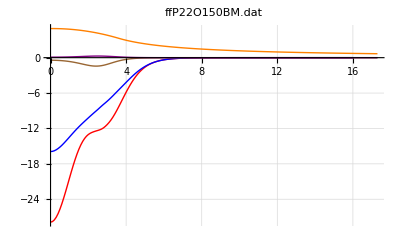

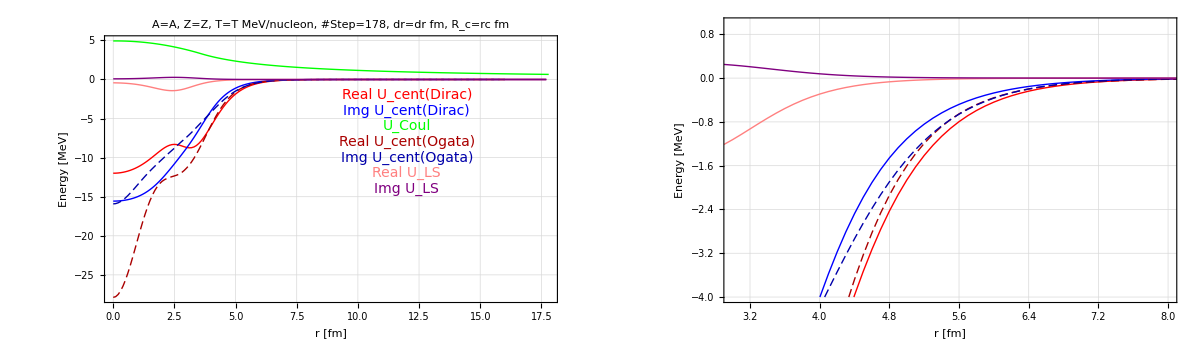

```mathematica
O22Dirac150=EDAD2[22,8,150,1.25,n,0.1,0];
O22Ogata150=GetOgata["ffP22O150BM.dat","DULS_22O150.dat",10,1];
CompareDiracOgata[O22Dirac150,O22Ogata150]
```

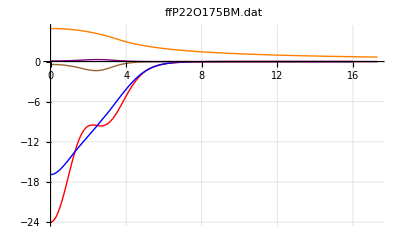

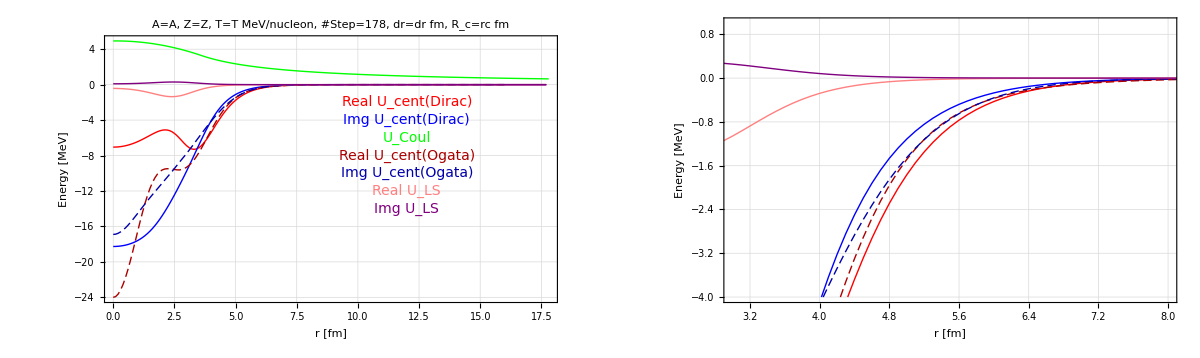

```mathematica
O22Dirac175=EDAD2[22,8,175,1.25,n,0.1,0];
O22Ogata175=GetOgata["ffP22O175BM.dat","DULS_22O175.dat",10,1];
CompareDiracOgata[O22Dirac175,O22Ogata175]
```

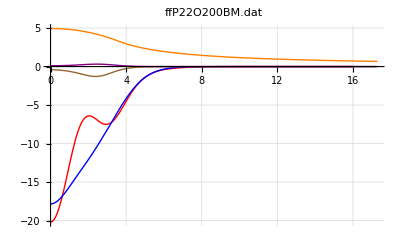

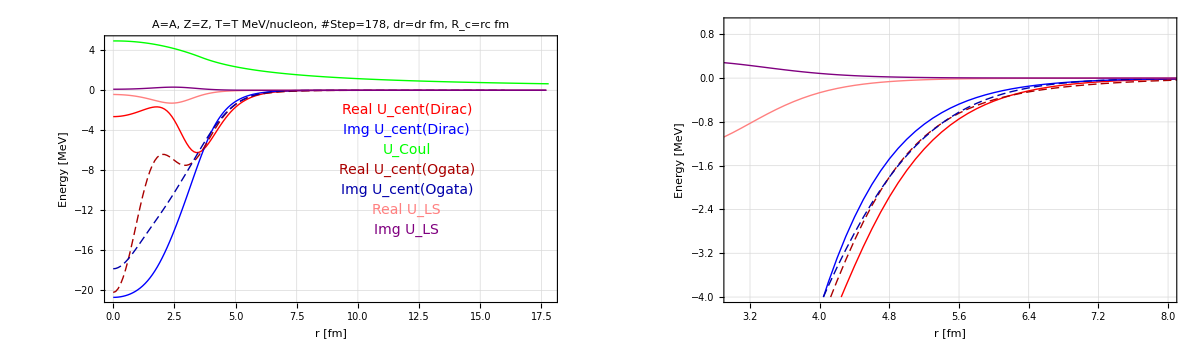

```mathematica
O22Dirac200=EDAD2[22,8,200,1.25,n,0.1,0];
O22Ogata200=GetOgata["ffP22O200BM.dat","DULS_22O200.dat",10,1];
CompareDiracOgata[O22Dirac200,O22Ogata200]
```

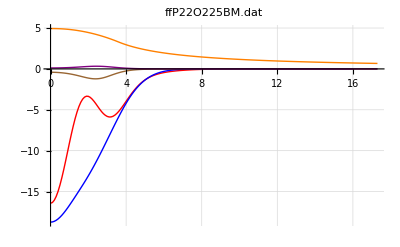

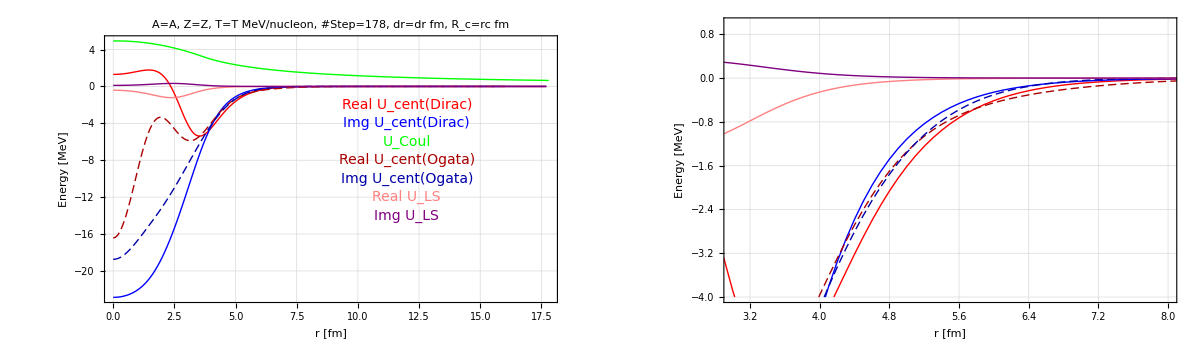

```mathematica
O22Dirac225=EDAD2[22,8,225,1.25,n,0.1,0];
O22Ogata225=GetOgata["ffP22O225BM.dat","DULS_22O225.dat",10,1];
CompareDiracOgata[O22Dirac225,O22Ogata225]
```

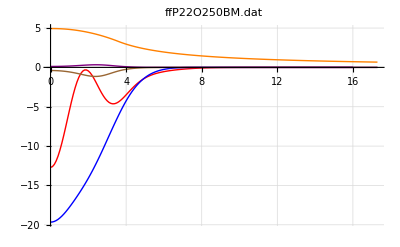

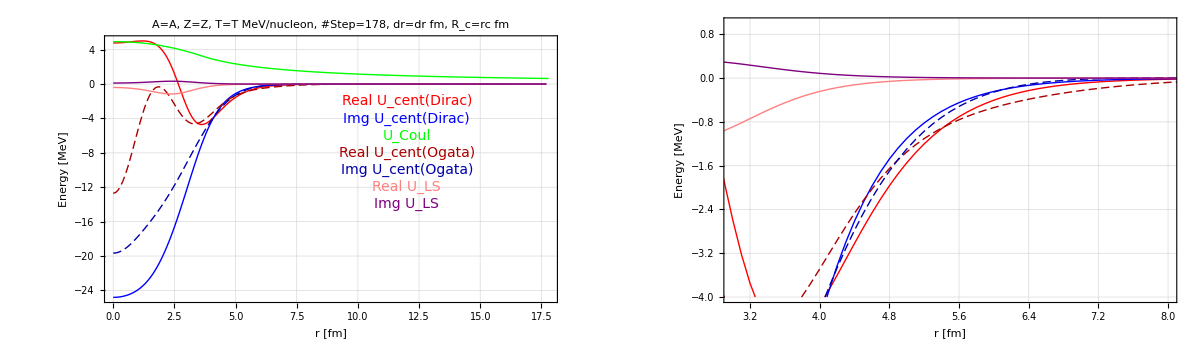

```mathematica
O22Dirac250=EDAD2[22,8,250,1.25,n,0.1,0];
O22Ogata250=GetOgata["ffP22O250BM.dat","DULS_22O250.dat",10,1];
CompareDiracOgata[O22Dirac250,O22Ogata250]
```

## With Ogata

```mathematica
GetOgata[filename_,LSfilename_,SkipRow_,Linux_]:=Module[
{RawData,n,DOgata,DLS,DCoul,dir,chdir},
dir=Directory[];
If[dir=="/home/goluckyryan/Dropbox/ExperimentDoc/[201206]SHARAQ04/DataAnalysis/Simulations/Ogata",chdir=0,Print["change dir."];chdir=1];
If[chdir==1,
If[Linux==1 ,
SetDirectory[Directory[]<>"/Dropbox/ExperimentDoc/[201206]SHARAQ04/DataAnalysis/Simulations/Ogata/"],
SetDirectory["D:/Dropbox/ExperimentDoc/[201206]SHARAQ04/DataAnalysis/Simulations/Ogata/"]
];
Print[Directory[]];
];
RawData=Drop[Import[filename],SkipRow];
n=Length[RawData];
DOgata=Table[{RawData [[i,1]],RawData[[i,2]]+ⅈ RawData[[i,3]]},{i,1,n}];
RawData=Drop[Import[LSfilename],SkipRow];
n=Length[RawData];
DLS=Table[{RawData [[i,1]],RawData[[i,2]]+ⅈ RawData[[i,3]]},{i,1,n}];
DCoul=Table[{RawData [[i,1]],RawData[[i,4]]},{i,1,n}];
Print[ListPlot[{
RePot[DOgata],
ImPot[DOgata],
RePot[DLS],
ImPot[DLS],
DCoul},Joined->True,PlotRange->All,PlotLabel->filename,PlotStyle->{Red,Blue,Brown,Purple,Orange},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted]]];
{DOgata,DLS,DCoul}
]
```

change dir.

/home/goluckyryan/Dropbox/ExperimentDoc/[201206]SHARAQ04/DataAnalysis/Simulations/Ogata

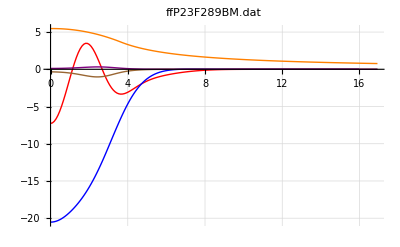

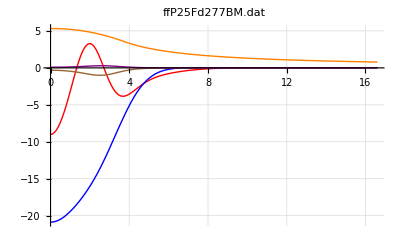

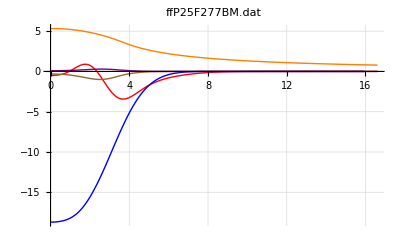

```mathematica
Ogata23F=GetOgata["ffP23F289BM.dat","DULS_23F289.dat",10,1];
Ogata25Fd=GetOgata["ffP25Fd277BM.dat","DULS_25F277.dat",10,1];
Ogata25Fs=GetOgata["ffP25F277BM.dat","DULS_25F277.dat",10,1];
```

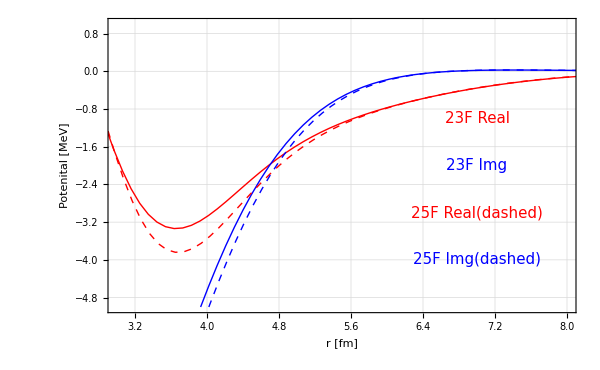

```mathematica
ListPlot[{
RePot[Ogata23F[[1]]],
ImPot[Ogata23F[[1]]],
RePot[Ogata25Fd[[1]]],
ImPot[Ogata25Fd[[1]]]
},Joined->True,PlotStyle->{Red,Blue,Directive[Red,Dashed], Directive[Blue,Dashed]},PlotRange->{{3,8},{-5,1}},
Frame->True,FrameLabel->{Style["r [fm]",20],Style["Potenital [MeV]",20]}, 
GridLines->Automatic, GridLinesStyle->Directive[Gray,Dotted], Axes->False,
ImageSize->600,
Epilog->{
Text[Style["23F Real",Red,15],{7,-1}],
Text[Style["23F Img",Blue,15],{7,-2}],
Text[Style["25F Real(dashed)",Red,15],{7,-3}],
Text[Style["25F Img(dashed)",Blue,15],{7,-4}]
}
]
```

```mathematica
CompareDiracOgata[potDirac_,potOgata_]:=Module[
{gA,gB},
gA=ListPlot[{
RePot[potDirac[[1]]],
ImPot[potDirac[[1]]],
potDirac[[4]],
RePot[potOgata[[1]]],
ImPot[potOgata[[1]]],
RePot[potDirac[[2]]],
ImPot[potDirac[[2]]]
},
Epilog->{
Text[Style["Real U_cent(Dirac)",Red,14],{12,-2}],
Text[Style["Img U_cent(Dirac)",Blue,14],{12,-4}],
Text[Style["U_Coul",Green,14],{12,-6}],
Text[Style["Real U_cent(Ogata)",Darker[Red],14],{12,-8}],
Text[Style["Img U_cent(Ogata)",Darker[Blue],14],{12,-10}],
Text[Style["Real U_LS",Pink,14],{12,-12}],
Text[Style["Img U_LS",Purple,14],{12,-14}]
},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Axes->False,
Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Green,Directive[Darker[Red],Dashing[{0.01,0.005}]],Directive[Darker[Blue],Dashing[{0.01,0.005}]],Pink,Purple},
Frame->True,FrameLabel->{Style["r [fm]",14],Style["Energy [MeV]",14]},
ImageSize->600,PlotLabel->Style["A="<>ToString[A]<>", Z="<>ToString[Z]<>", T="<>ToString[T]<>" MeV/nucleon, \n#Step="<>ToString[n]<>", dr="<>ToString[dr]<>" fm, R_c="<>ToString[rc]<>" fm",20]];
gB=ListPlot[{
RePot[potDirac[[1]]],
ImPot[potDirac[[1]]],
potDirac[[4]],
RePot[potOgata[[1]]],
ImPot[potOgata[[1]]],
RePot[potDirac[[2]]],
ImPot[potDirac[[2]]]
},
GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],Axes->False,
Joined->True,PlotRange->{{3,8},{-4,1}},
PlotStyle->{Red,Blue,Green,Directive[Darker[Red],Dashing[{0.01,0.005}]],Directive[Darker[Blue],Dashing[{0.01,0.005}]],Pink,Purple},
Frame->True,FrameLabel->{Style["r [fm]",14],Style["Energy [MeV]",14]},
ImageSize->600];
GraphicsGrid[{{gA,gB}},ImageSize->1200]
]
```

## Check potl*.dat

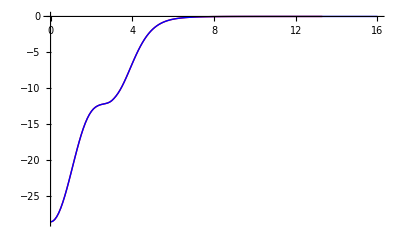

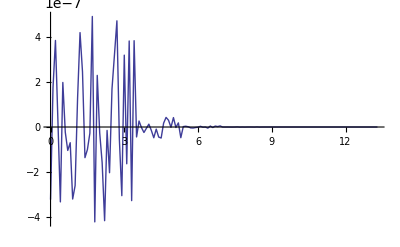

{}

```mathematica
ntlab=4;
Data=Take[Drop[Import["25F277d_c_B.dat"],7+(ntlab-1) 135],134];
Data2=Drop[Import["DULS_24O150.dat"],10];
Data2=Drop[Import["ffP24Od150BM.dat"],10];
Col1=1;
Col2=2;
Data1=Table[
If[!NumberQ[Data[[i,j]]],
ToExpression[StringReplace[Data[[i,j]],{
"("->"",")"->"",
","->"",
"E+00"->"",
"E+01"->"*10",
"E-01"->"*0.1",
"E-02"->"*0.01",
"E-03"->"*0.001",
"E-04"->"*0.0001",
"E-05"->"*0.00001",
"E-06"->"*0.000001",
"E-07"->"*0.0000001",
"E-08"->"*0.00000001",
"E-09"->"*0.000000001"}]],
Data[[i,j]]],{i,1,Length[Data]},{j,1,5}];
Data1=Table[Join[{(i-1)0.1},Data1[[i]]],{i,1,Length[Data1]}];
ListPlot[{
Table[Data1[[i,{1,Col1+1}]],{i,1,Length[Data1]}],
Table[Data2[[i,{1,Col2}]],{i,1,Length[Data2]}]
},Joined->True,PlotRange->All,PlotStyle->{Red,Blue}]
ListPlot[{
Table[{Data1[[i,1]],Data2[[i,Col2]]-Data1[[i,Col1+1]]},{i,1,Length[Data1]}]
},Joined->True,PlotRange->All]
Select[Table[{Data1[[i,1]],Data2[[i,Col2]]-Data1[[i,Col1+1]]},{i,1,Length[Data1]}],#[[2]]>1 &]
```

## Density

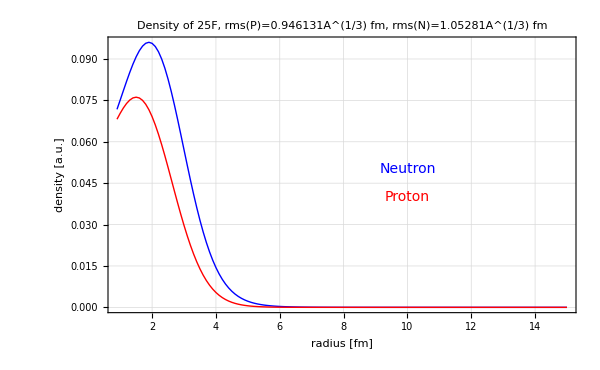

```mathematica
(* Density *)
A=25;
Z=9;
Ogata=Drop[Import["den25F_d.dat"],10];
OgataN=Table[Ogata[[i,{1,2}]],{i,1,Length[Ogata]}];
OgataP=Table[Ogata[[i,{1,3}]],{i,1,Length[Ogata]}];
ListPlot[{OgataN,OgataP},Joined->True,PlotRange->All,Frame->True,FrameLabel->{Style[" radius [fm]",20],Style["density [a.u.]",20]},ImageSize->600,
PlotLabel->Text[Style["Density of "<>ToString[A]<>If[Z==9,"F","O"]<>", \nrms(P)="<>ToString[RMS[OgataP]/A^(1/3)]<>"A^(1/3) fm, rms(N)="<>ToString[RMS[OgataN]/A^(1/3)]<>"A^(1/3) fm",20]],GridLines->Automatic,GridLinesStyle->Directive[Gray,Dotted],PlotStyle->{Blue,Red},
Epilog->{Text[Style["Neutron",Blue,14],{10,0.05}],Text[Style["Proton",Red,14],{10,0.04}]}]
```

## Plane wave Born Approximation - Elastic scattering

```mathematica
PWBA[U_,r_,q_]:=mp/ℏ^2 U r Sin[q r]/q
```

3.6537

1.71968

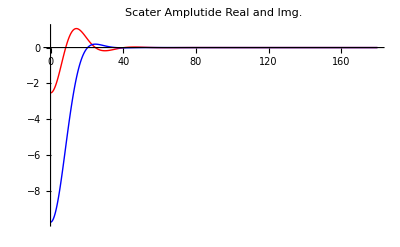

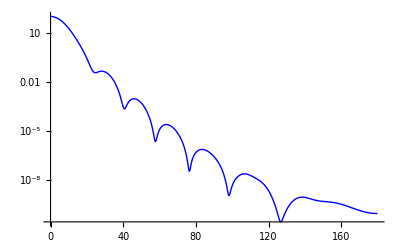

```mathematica
(* scatter amplitude f[θ] ∝ NIntegrate[V[r] r Sin[q r] ,{r,0,n dr}], q = k'-k*)
k=(√(2mp T))/ℏ(* fm^-1 *)
λ=2 π/k(* fm *)
dθ=0.001;
Dθ=Table[θ,{θ,0.00001,π,dθ}];
Dq=Table[2 k Sin[Dθ[[i]]/2],{i,1,Length[Dθ]}];
fUcent=Table[{Dθ[[p]] 180/π,Sum[PWBA[DUcent[[i,2]],(DR[[i]]+DR[[i+1]])/2, Dq[[p]] ]dr,{i,1,n-1}]},{p,1,Length[Dθ]}];
fUcentR=Table[{fUcent[[p,1]],Re[fUcent[[p,2]]]},{p,1,Length[Dθ]}];
fUcentI=Table[{fUcent[[p,1]],Im[fUcent[[p,2]]]},{p,1,Length[Dθ]}];
fUcentM=Table[{fUcent[[p,1]],Norm[fUcent[[p,2]]]^2},{p,1,Length[Dθ]}];

ListPlot[{fUcentR,fUcentI},Joined->True,PlotStyle->{Red,Blue,Green},PlotRange->All,PlotLabel->"Scater Amplutide Real and Img."]
ListLogPlot[{fUcentM},Joined->True,PlotStyle->{Blue},PlotRange->All]
```

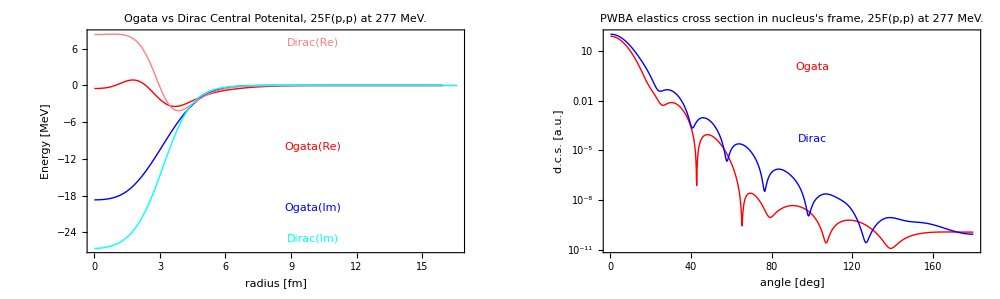

```mathematica
(*Mass=Sum[DOgata[[i,2]] DR[[i]]^2 dr,{i,1,n}]
RMS=√(Sum[DOgata[[i,2]] DR[[i]]^2 dr,{i,1,n}]/Sum[DOgata[[i,2]]dr,{i,1,n}])*)
p1=ListPlot[{DOgataR,DOgataI,DUcentR,DUcentI}, PlotStyle->{Red,Blue,Pink,Cyan},
Epilog->{
Text[Style["Ogata(Re)",Red],{10,-10}],
Text[Style["Ogata(Im)",Blue],{10,-20}],
Text[Style["Dirac(Re)",Pink],{10,7}],
Text[Style["Dirac(Im)",Cyan],{10,-25}]},Joined->True, PlotRange->All,
PlotLabel->"Ogata vs Dirac Central Potenital, \n"<>ToString[A]<>If[Z==9,"F(p,p) at ","O(p,p)"]<>ToString[T]<>" MeV.",
Frame->True, 
FrameLabel->{"radius [fm]","Energy [MeV]"}];
fOgata=Table[{Dθ[[p]] 180/π,Norm[Sum[PWBA[DOgata[[i,2]]+ⅈ DOgata[[i,3]],DR[[i]],Dq[[p]] ]dr,{i,1,Length[DOgata]}]]^2},{p,1,Length[Dθ]}];
p2=ListLogPlot[{fOgata,fUcentM}, PlotStyle->{Red,Blue},
Epilog->{
Text[Style["Ogata",Red],{100,0}],
Text[Style["Dirac",Blue],{100,-10}]},Joined->True,
PlotLabel->"PWBA elastics cross section in nucleus's frame, \n"<>ToString[A]<>If[Z==9,"F(p,p) at ","O(p,p)"]<>ToString[T]<>" MeV.",
Frame->True, 
FrameLabel->{"angle [deg]","d.c.s. [a.u.]"}];
GraphicsGrid[{{p1,p2}},ImageSize->1000]
```

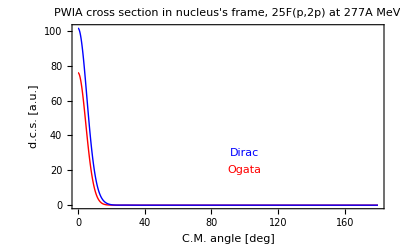

```mathematica
ListPlot[{fOgata,fUcentM}, PlotStyle->{Red,Blue},
Epilog->{
Text[Style["Ogata",Red],{100,20}],
Text[Style["Dirac",Blue],{100,30}]},Joined->True,PlotRange->All,
PlotLabel->"PWIA cross section in nucleus's frame, \n"<>ToString[A]<>"F(p,2p) at "<>ToString[T]<>"A MeV.",
Frame->True, 
FrameLabel->{"C.M. angle [deg]","d.c.s. [a.u.]"}]
```

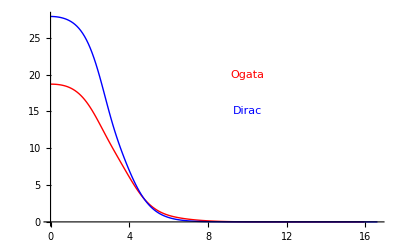

```mathematica
DOgataM=Table[{DR[[i]],Norm[DOgata[[i,2]]+ⅈ DOgata[[i,3]]]},{i,1,Length[DOgata]}];
DUcentM=Table[{DR[[i]],Norm[DUcent[[i,2]]]},{i,1,n}];
ListPlot[{DOgataM,DUcentM},Joined->True, PlotStyle->{Red,Blue},
Epilog->{
Text[Style["Ogata",Red],{10,20}],
Text[Style["Dirac",Blue],{10,15}]}]
```